```mathematica
μ0 = 4π*10^-7; (*N/A^2*)
ρCu=1.68*10^-8; (*Ohm m*)
densityCu=8960 ;(*kg m^-3*)
specificheatcapacityCu=385 ;(*J kg^-1 K^-1*)
volumetricheatcapacity=densityCu*specificheatcapacityCu ; (*J m^-3 K^-1*)
```

```mathematica
(*Tesla*)
Bcoil[z_,zpos_,turns_, radius_, current_]:= (μ0*current*turns)/2 radius^2/((radius^2+(zpos-z)^2)^(3/2)) ; 
(*Tesla/m*)
dBdzcoil[z_,zpos_,turns_, radius_, current_]:= (3 *μ0*current*turns)/2 radius^2/((radius^2+(zpos-z)^2)^(5/2)) (zpos-z); 
(*Tesla, total dimensions of rectangular coil are width = 2*lx and height = 2*ly *)
Brect[z_, zpos_, turns_, lx_,ly_, current_]:=(μ0*current*turns)/(4π) (1/(√(lx^2+ly^2+(zpos-z)^2)))((2*lx)/(√(lx^2+ly^2+(zpos-z)^2)-ly)+(2*ly)/(√(lx^2+ly^2+(zpos-z)^2)-lx)-(2*ly)/(√(lx^2+ly^2+(zpos-z)^2)+lx)-(2*lx)/(√(lx^2+ly^2+(zpos-z)^2)+ly))
```

```mathematica
(*MOT is at z=0mm*)
(* Two square coils*)
Manipulate[
Show[Plot[{( Brect[z*10^-3,pos1*10^-3,turns1,lx1*10^-3,ly1*10^-3,curr1]+ Brect[z*10^-3,pos2*10^-3,turns2,lx2*10^-3,ly2*10^-3,-1*curr2])*10^4,7.14-1.7/10 z},{z,-200,200},PlotRange->{{-20,20},{0,10}},Frame->True,FrameLabel->{"Position (mm)","B field (G)"},PlotLabel->"Coil 1: Power dissapation = "<>ToString[ρCu*(turns1*2*(2*lx1*10^-3+2*ly1*10^-3))/((1/8*2.54*10^-2)^2-(1/16*2.54*10^-2)^2) curr1^2]<>" W 
ΔTemp/min = "<>ToString[(ρCu*(turns1*2*(2*lx1*10^-3+2*ly1*10^-3))/((1/8*2.54*10^-2)^2-(1/16*2.54*10^-2)^2) curr1^2)/(turns1*2*(2*lx1*10^-3+2*ly1*10^-3)*((1/8*2.54*10^-2)^2-(1/16*2.54*10^-2)^2)*volumetricheatcapacity)*60]<>" K/min 
Voltage = "<>ToString[curr1 * ρCu*(turns1*2*(2*lx1*10^-3+2*ly1*10^-3))/((1/8*2.54*10^-2)^2-(1/16*2.54*10^-2)^2)]<>" V
Coil 2: Power dissapation = "<>ToString[ρCu*(turns2*2*(2*lx2*10^-3+2*ly2*10^-3))/((1/8*2.54*10^-2)^2-(1/16*2.54*10^-2)^2) curr2^2]<>" W 
ΔTemp/min = "<>ToString[(ρCu*(turns2*2*(2*lx2*10^-3+2*ly2*10^-3))/((1/8*2.54*10^-2)^2-(1/16*2.54*10^-2)^2) curr2^2)/(turns2*2*(2*lx2*10^-3+2*ly2*10^-3)*((1/8*2.54*10^-2)^2-(1/16*2.54*10^-2)^2)*volumetricheatcapacity)*60]<>" K/min 
Voltage = "<>ToString[curr2* ρCu*(turns2*2*(2*lx2*10^-3+2*ly2*10^-3))/((1/8*2.54*10^-2)^2-(1/16*2.54*10^-2)^2)]<>" V
Residual B field at MOT"],
Plot[(D[(Brect[z*10^-3,pos1*10^-3,turns1,lx1*10^-3,ly1*10^-3,curr1]+Brect[z*10^-3,pos2*10^-3,turns2,lx2*10^-3,ly2*10^-3,-1*curr2])*10^4,z]/.z->0) u+7.14,{u,-20,20},PlotStyle->{Dashed},Frame->True]], 
{{turns1,4},1, 20,1},{{pos1,-55},-60, -20},{{lx1,115},100, 125 },{{ly1,125},115, 150 },{{turns2,4},1, 20,1},{{pos2,55},20,60},{{lx2,115},100,125},{{ly2,125},115,150},{{curr1,95},1,220},{{curr2,47},1,80}]
```

```mathematica
N[4*2*(2*115*10^-3+2*125*10^-3)]
```

3.84

```mathematica
ρCu*(4*2*(2*115*10^-3+2*125*10^-3))/((1/8*2.54*10^-2)^2-(1/16*2.54*10^-2)^2)
```

0.0085328

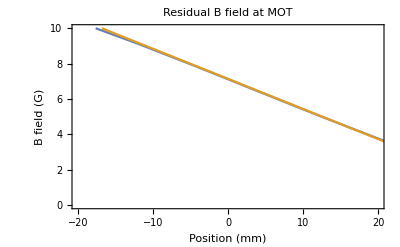

```mathematica
turns1=4;
turns2=4;
pos1=-55;
pos2=55;
lx1=115;
ly1=125;
lx2=115;
ly2=125;
curr1=95;
curr2=47;
Plot[{( Brect[z*10^-3,pos1*10^-3,turns1,lx1*10^-3,ly1*10^-3,curr1]+ Brect[z*10^-3,pos2*10^-3,turns2,lx2*10^-3,ly2*10^-3,-1*curr2])*10^4,7.14-1.7/10 z},{z,-200,200},PlotRange->{{-20,20},{0,10}},PlotLabel->"Residual B field at MOT",FrameLabel->{"Position (mm)","B field (G)"},Frame->True]
```

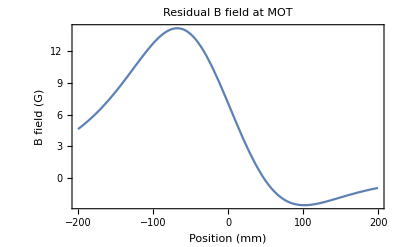

```mathematica
Plot[{( Brect[z*10^-3,pos1*10^-3,turns1,lx1*10^-3,ly1*10^-3,curr1]+ Brect[z*10^-3,pos2*10^-3,turns2,lx2*10^-3,ly2*10^-3,-1*curr2])*10^4},{z,-200,200},PlotRange->All,PlotLabel->"Residual B field at MOT",FrameLabel->{"Position (mm)","B field (G)"},Frame->True]
```